```mathematica
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"]
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\DiscreteNashEqulibrium.wl"]
```

{{{1,0},{0,1}},{{1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,1/2-ⅈ/2}},{{-1/2+ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2-ⅈ/2}},{{-1,0},{0,-1}},{{-1/2-ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,-1/2+ⅈ/2}},{{1/2-ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,1/2+ⅈ/2}},{{ⅈ,0},{0,-ⅈ}},{{-1/2+ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2-ⅈ/2}},{{-1/2-ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,-1/2+ⅈ/2}},{{-ⅈ,0},{0,ⅈ}},{{1/2-ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,1/2+ⅈ/2}},{{1/2+ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,1/2-ⅈ/2}},{{0,1},{-1,0}},{{-1/2+ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2-ⅈ/2}},{{-1/2+ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,-1/2-ⅈ/2}},{{0,-1},{1,0}},{{1/2-ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,1/2+ⅈ/2}},{{1/2-ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,1/2+ⅈ/2}},{{0,ⅈ},{ⅈ,0}},{{-1/2-ⅈ/2,1/2+ⅈ/2},{-1/2+ⅈ/2,-1/2+ⅈ/2}},{{-1/2-ⅈ/2,1/2-ⅈ/2},{-1/2-ⅈ/2,-1/2+ⅈ/2}},{{0,-ⅈ},{-ⅈ,0}},{{1/2+ⅈ/2,-1/2-ⅈ/2},{1/2-ⅈ/2,1/2-ⅈ/2}},{{1/2+ⅈ/2,-1/2+ⅈ/2},{1/2+ⅈ/2,1/2-ⅈ/2}}}

```mathematica
su2[0,0,0]
```

{{1,0},{0,1}}

```mathematica
T = DeleteDuplicates[binaryTetrahedralGroup//ComplexExpand,(#1==#2||#1==-#2)&];
```

```mathematica
Table[i//MatrixForm,{i,T//ComplexExpand}]
```

{(1 | 0
0 | 1),(1/2+ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | 1/2-ⅈ/2),(-1/2+ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | -1/2-ⅈ/2),(ⅈ | 0
0 | -ⅈ),(-1/2+ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | -1/2-ⅈ/2),(-1/2-ⅈ/2 | -1/2+ⅈ/2
1/2+ⅈ/2 | -1/2+ⅈ/2),(0 | 1
-1 | 0),(-1/2+ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | -1/2-ⅈ/2),(-1/2+ⅈ/2 | -1/2-ⅈ/2
1/2-ⅈ/2 | -1/2-ⅈ/2),(0 | ⅈ
ⅈ | 0),(-1/2-ⅈ/2 | 1/2+ⅈ/2
-1/2+ⅈ/2 | -1/2+ⅈ/2),(-1/2-ⅈ/2 | 1/2-ⅈ/2
-1/2-ⅈ/2 | -1/2+ⅈ/2)}

THis seems to behave correctly, but technichally these arent all elements of su2, since they dont have det 1 (but -1)

```mathematica
σ0= ({{1, 0}, {0, 1}});σ1 = ({{0, 1}, {1, 0}});σ2 = ({{0, -I}, {I, 0}});σ3 = ({{1, 0}, {0, -1}});s =  ({{1, 0}, {0, I}});
D4 = {σ0,σ3,s,s.σ3,s.σ1,s.σ2,σ1,σ2};
D4 = {σ0,σ3,s,s.σ3,s.σ1,s.σ2,σ1,σ2};
D4Sym = {"σ_0","σ_z","S","Sσ_z","Sσ_x","Sσ_y","σ_x","σ_y"};
```

```mathematica
Table[i//MatrixForm,{i,D4}]
```

{(1 | 0
0 | 1),(0 | 1
-1 | 0),((1+ⅈ)/(√2) | 0
0 | (1-ⅈ)/(√2)),(0 | (1+ⅈ)/(√2)
-(1-ⅈ)/(√2) | 0),(ⅈ | 0
0 | -ⅈ),(0 | ⅈ
ⅈ | 0),(-(1-ⅈ)/(√2) | 0
0 | -(1+ⅈ)/(√2)),(0 | -(1-ⅈ)/(√2)
(1+ⅈ)/(√2) | 0)}

## a=b=0 γ=π/2

```mathematica
strategyGroup = D4;
symmetricJ = FullSimplify[(J[0,0,Pi/2]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,8},{j,8}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

```mathematica
simplifiedEQ= (FullSimplify[{#[[1]],#[[2]],Reduce[#[[3]]]},Assumptions->0<γ<π/2]&/@eq);
```

```mathematica
simplifiedEQ
```

{}

## a=b=0

```mathematica
strategyGroup = D4
```

{{{1,0},{0,1}},{{0,1},{-1,0}},{{(1+ⅈ)/(√2),0},{0,(1-ⅈ)/(√2)}},{{0,(1+ⅈ)/(√2)},{-(1-ⅈ)/(√2),0}},{{ⅈ,0},{0,-ⅈ}},{{0,ⅈ},{ⅈ,0}},{{-(1-ⅈ)/(√2),0},{0,-(1+ⅈ)/(√2)}},{{0,-(1-ⅈ)/(√2)},{(1+ⅈ)/(√2),0}}}

```mathematica
symmetricJ = FullSimplify[(J[0,0,γ]//FullSimplify),Assumptions->0<γ<π/2];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,strategyGroup[[i]],strategyGroup[[j]]],{i,8},{j,8}]/.Conjugate->MyConj];
```

```mathematica
alicesScores = FullSimplify[(Map[alicesScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
bobsScores = FullSimplify[(Map[bobsScore,finalStates,{2}]/.Conjugate->MyConj)//Simplify];
```

```mathematica
alicesScores//MatrixForm
```

(3 | 0 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 2+Cos[2 γ] | 5 Sin[γ]^2 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2
5 | 1 | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 Cos[γ]^2 | 2-Cos[2 γ] | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ])
1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 2+Cos[2 γ] | 0 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 3 | 5 Sin[γ]^2
5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 | 2-Cos[2 γ] | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 Cos[γ]^2 | 1
2+Cos[2 γ] | 5 Sin[γ]^2 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 3 | 0 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2
5 Cos[γ]^2 | 2-Cos[2 γ] | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 | 1 | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ])
1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 3 | 5 Sin[γ]^2 | 1/2 (5+Cos[2 γ]) | (5 Sin[γ]^2)/2 | 2+Cos[2 γ] | 0
5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 Cos[γ]^2 | 1 | 5/4 (3+Cos[2 γ]) | 1/2 (3-Cos[2 γ]) | 5 | 2-Cos[2 γ])

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),0<γ<Pi/2];
```

```mathematica
eq//MatrixForm
```

({2,6} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)]
{4,4} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)]
{6,2} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)]
{8,8} | {2-Cos[2 γ],2-Cos[2 γ]} | 0<γ≤2 ArcTan[√(5-2 √6)])

```mathematica
Manipulate[MatrixPlot[alicesScores/.γ->g],{{g,2 ArcTan[√(5-2 √6)]},0,Pi/2}]
```

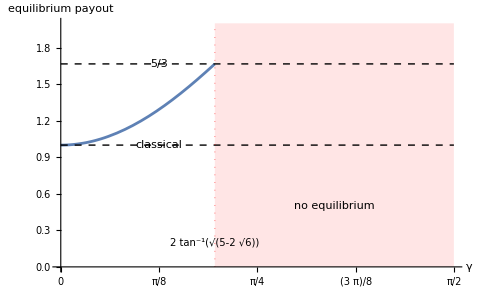

```mathematica
val=2 ArcTan[Sqrt[5-2 Sqrt[6]]];

Plot[Piecewise[{{2-Cos[2 γ],γ<=val}},-1],{γ,0,Pi/2},PlotRange->{0,2},AxesLabel->{"γ","equilibrium payout"},Ticks->{Range[0,Pi/2,Pi/8],Automatic},Prolog->{{Red,Opacity[0.1],Rectangle[{val,0},{Pi/2,2}]}},Epilog->{(*Horizontal Lines*){Dashed,Thin,Line[{{0,1},{Pi/2,1}}]},{Dashed,Thin,Line[{{0,5/3},{Pi/2,5/3}}]},(*Labels*)Text["classical",{Pi/8,1},{0,-1.5}],Text["5/3",{Pi/8,5/3},{0,-1.5}],Text["no equilibrium",{(val+Pi/2)/2,0.5}],(*Vertical Line and Formula Label*){Red,Dotted,Opacity[0.5],Line[{{val,0},{val,2}}]},Text[Style[HoldForm[2 ArcTan[Sqrt[5-2 Sqrt[6]]]],10],{val,0.2},{1.2,0}]}]
```

## (a=b) != 0

```mathematica
assumptions = 0<γ<π/2&&-Infinity<a<Infinity;
```

```mathematica
symmetricJ = FullSimplify[(J[a,a,γ]//FullSimplify),Assumptions->assumptions];
```

```mathematica
finalStates = FullSimplify[Table[play[symmetricJ,D4[[i]],D4[[j]]],{i,8},{j,8}]/.Conjugate->MyConj,Assumptions->assumptions];
```

```mathematica
alicesScores = FullSimplify[(ParallelMap[alicesScore,finalStates,{2}])//Simplify];
bobsScores = FullSimplify[(ParallelMap[bobsScore,finalStates,{2}])//Simplify];
```

```mathematica
alicesScores//MatrixForm
```

(3 | 0 | 1/8 (21-Cos[2 a γ]+Cos[2 γ] (-3+7 Cos[2 a γ])) | 1/2 (5 Cos[a γ]^2 Sin[γ]^2+(2+Cos[2 γ]) Sin[a γ]^2) | 3 Cos[γ]^2 Cos[a γ]^2+(3-2 Cos[2 a γ]) Sin[γ]^2 | 5 Cos[a γ]^2 Sin[γ]^2+(2+Cos[2 γ]) Sin[a γ]^2 | 1/8 (21-Cos[2 a γ]+Cos[2 γ] (-3+7 Cos[2 a γ])) | 1/2 (5 Cos[a γ]^2 Sin[γ]^2+(2+Cos[2 γ]) Sin[a γ]^2)
5 | 1 | 1/8 (29+Cos[2 a γ]+Cos[2 γ] (3+7 Cos[2 a γ])) | 1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ]) | Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2 | Cos[γ]^2 (3-2 Cos[2 a γ])+3 Cos[a γ]^2 Sin[γ]^2 | 1/8 (29+Cos[2 a γ]+Cos[2 γ] (3+7 Cos[2 a γ])) | 1/8 (13+3 Cos[2 γ]-(1+7 Cos[2 γ]) Cos[2 a γ])
7/8 (3+Cos[2 γ])-1/8 (1+3 Cos[2 γ]) Cos[2 a γ] | 1/2 (5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2) | 1/32 (69+16 Cos[2 γ]+8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]+8 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]) | -1/8 (-17+Cos[2 a γ]+8 Cos[a γ] Sin[γ]) Sin[a γ]^2 | 1/8 (6 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+(-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2) | 1/8 (5 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+6 (2+Cos[2 γ]+Cos[2 a γ]) Sin[a γ]^2+4 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2) | 1/32 (85+12 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (75-40 Cos[2 γ]-20 Cos[2 (-1+a) γ]+4 Cos[2 a γ]+Cos[4 a γ]-20 Cos[2 (1+a) γ]-48 Sin[γ] Sin[a γ] Sin[2 a γ])
1/2 (5+Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2) | 1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]) | 1/32 (115+44 Cos[2 a γ]+Cos[4 a γ]-16 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/2 (5 Cos[a γ]^4+Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2-3 Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2) | 1/16 (35+6 Cos[2 γ]-7 Cos[2 (-1+a) γ]-10 Cos[2 a γ]-Cos[4 a γ]-7 Cos[2 (1+a) γ]+24 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (75+80 Cos[2 γ] Cos[a γ]^2+4 Cos[2 a γ]+Cos[4 a γ]-32 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]+40 Sin[γ] Sin[a γ] Sin[2 a γ])
-Cos[γ]^2 (-4+Cos[2 a γ])+Cos[a γ]^2 Sin[γ]^2 | 5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2 | 1/16 (35+14 Cos[2 γ]-Cos[4 a γ]+4 Sin[γ] (-Cos[a γ]+Cos[3 a γ]+3 Cos[2 a γ] Sin[γ])) | 1/16 (37-18 Cos[2 a γ]-2 Cos[2 γ] (7+3 Cos[2 a γ])+Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]) | 17/8+Cos[2 a γ]-1/8 Cos[4 a γ] | 5 Sin[a γ]^4+Sin[2 a γ]^2 | 1/16 (35+14 Cos[2 γ]-3 Cos[2 (-1+a) γ]+6 Cos[2 a γ]-Cos[4 a γ]-3 Cos[2 (1+a) γ]+8 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/16 (37-18 Cos[2 a γ]-2 Cos[2 γ] (7+3 Cos[2 a γ])+Cos[4 a γ]-16 Sin[γ] Sin[a γ] Sin[2 a γ])
Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2 | Cos[γ]^2 Cos[a γ]^2-(-4+Cos[2 a γ]) Sin[γ]^2 | 1/2 (5 Cos[a γ]^4+Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2+Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2) | 1/8 (35/2-5 Cos[2 a γ]+Cos[2 γ] (-7+3 Cos[2 a γ])-1/2 Cos[4 a γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]) | 5 Cos[a γ]^4+Sin[2 a γ]^2 | 1/8 (17-8 Cos[2 a γ]-Cos[4 a γ]) | 1/2 (5 Cos[a γ]^4+Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2-Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2) | 1/8 (2 Cos[a γ]^2 (2+Cos[2 γ]+Cos[2 a γ])+3 (-1+Cos[2 a γ]+2 Cos[a γ] Sin[γ])^2+20 (Cos[a γ]+Sin[γ])^2 Sin[a γ]^2)
7/8 (3+Cos[2 γ])-1/8 (1+3 Cos[2 γ]) Cos[2 a γ] | 1/2 (5 Cos[a γ]^2 Sin[γ]^2-(-2+Cos[2 γ]) Sin[a γ]^2) | 1/32 (85+12 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (75-40 Cos[2 γ]-20 Cos[2 (-1+a) γ]+4 Cos[2 a γ]+Cos[4 a γ]-20 Cos[2 (1+a) γ]+48 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/16 (35+6 Cos[2 a γ]+2 Cos[2 γ] (-3+7 Cos[2 a γ])-Cos[4 a γ]-32 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/16 (37-18 Cos[2 a γ]-2 Cos[2 γ] (3+7 Cos[2 a γ])+Cos[4 a γ]+32 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (69+16 Cos[2 γ]+8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]+8 Cos[2 (1+a) γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ]) | -1/8 (-17+Cos[2 a γ]-8 Cos[a γ] Sin[γ]) Sin[a γ]^2
1/2 (5+Cos[γ]^2 (4+Cos[2 a γ])+Sin[γ]^2 Sin[a γ]^2) | 1/8 (13-7 Cos[2 γ]+(-1+3 Cos[2 γ]) Cos[2 a γ]) | 1/32 (75+80 Cos[2 γ] Cos[a γ]^2+4 Cos[2 a γ]+Cos[4 a γ])+Sin[γ] Sin[a γ] Sin[2 a γ] | 1/32 (53-20 Cos[2 a γ]-Cos[4 a γ]-40 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/2 (5 Cos[a γ]^4+Cos[γ]^2 (3+2 Cos[2 a γ])+3 Sin[γ]^2 Sin[a γ]^2+3 Sin[γ] Sin[a γ] Sin[2 a γ]+Sin[2 a γ]^2) | 1/16 (35+Cos[2 γ] (6-14 Cos[2 a γ])-10 Cos[2 a γ]-Cos[4 a γ]-24 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (115+44 Cos[2 a γ]+Cos[4 a γ]+16 Sin[γ] Sin[a γ] Sin[2 a γ]) | 1/32 (69-16 Cos[2 γ]-8 Cos[2 (-1+a) γ]-4 Cos[2 a γ]-Cos[4 a γ]-8 Cos[2 (1+a) γ]-8 Sin[γ] Sin[a γ] Sin[2 a γ]))

Convert to γ′ == Sin[γ]^2  a′ = Sin[γ a]^2  for simplification

```mathematica
alicesScores = (((alicesScores/.a->ArcSin[Sqrt[a′]]/γ)/.γ->ArcSin[Sqrt[γ′]]))//TrigExpand//FullSimplify;
bobsScores = (((bobsScores/.a->ArcSin[Sqrt[a′]]/γ)/.γ->ArcSin[Sqrt[γ′]]))//TrigExpand//FullSimplify;
```

```mathematica
assumptions′ = 0<γ′<1&&0<a′<1;
```

```mathematica
eq = DiscreteNashEquilibria[(alicesScores),(bobsScores),assumptions′];
eq = DeleteCases[eq,{_,_,False}];
```

```mathematica
eq = ((#[[{1,2}]]~Join~{Simplify[Reduce[Simplify[#[[3]],assumptions′]]]}&/@eq)/.Reduce->Identity);
```

```mathematica
eq = DeleteCases[eq,{_,_,False}];
```

```mathematica
γOrig[γ_]:=ArcSin[Sqrt[γ]];
aOrig[γ_,a_]:=ArcSin[Sqrt[a]]/ArcSin[Sqrt[γ]]
```

```mathematica
eq/.{a′->a,γ′->g}//MatrixForm
```

({2,2} | {1,1} | (7 g<1&&(2+3 a) g≤a&&1+3 a g≥a+5 g)||(7 g==1&&2 a==1)
{2,5} | {a+5 g-3 a g,5-5 g+a (-4+7 g)} | (a==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&g+AlgebraicNumber-0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 g≤1&&(3 a≥5||(a>Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+3 a g≤a+5 g)))||((-1+a)/(-5+3 a)≤g&&((a>Root0.630Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&a≤Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(a (-10+a+11 a^2))/(5-7 a)^2+6 √2 √((a^3 (5-10 a+4 a^2+a^3))/(5-7 a)^4)+g≤0)||(a>Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&a≤Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&8 √((a^2 (32-92 a+112 a^2-75 a^3+23 a^4))/(8-7 a)^4)+g≤(32-60 a+68 a^2-39 a^3)/(8-7 a)^2)))
{2,6} | {1+2 g+a (-1+3 g),1+a (4-7 g)+2 g} | (a==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 g==1)||(8+3 a==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 g==23+3 √5)||(3 √5+2 a>7&&((a<Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(a (-2+23 a-11 a^2))/(2-7 a)^2+6 √2 √((a^3 (-1+8 a-8 a^2+a^3))/(2-7 a)^4)≤g&&3 g≤1)||(a>0&&8+3 a<3 √5+√(151-66 √5)&&a/(2+3 a)≤g&&6 √2 √((a^3 (-1+8 a-8 a^2+a^3))/(2-7 a)^4)+g≤(a (-2+23 a-11 a^2))/(2-7 a)^2)))||(3 g≤1&&(((2+3 a) g≥a&&3 √5+2 a≤7)||2+3 a≤0))
{2,8} | {1+g+1/2 a (-1+3 g),1+a (2-(7 g)/2)+g} | a==(2 g)/(1-3 g)&&Im[g]==0&&(3 Re[g]>1||Re[g]≤AlgebraicNumber0.0837AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762)
{4,4} | {1/4 (4-a^2+2 a (3+√(1-a) √g-4 g)+8 g),1/4 (4-a^2+2 a (3+√(1-a) √g-4 g)+8 g)} | (2+3 a==0&&54 g≤17+√145)||(a==Root-0.590Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324&&g==1/72 ((-24+12 a-13 a^2)/(-1+a)+5 √((a^2 (48-24 a+a^2))/(-1+a)^2)))||(a==Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&6916252 g+3 √(7 (351156463431424-5958129102912 Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694-68154041956 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^2+225248900 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^3+13811831 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^4))==1372 (101154-131684 Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259-248261 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^2+28136 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^3+432572 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^4))||(1/2 ((a (4+9 a+2 a^2))/(2+3 a)^2-√(-(a^3 (-8-9 a+12 a^2+5 a^3))/(2+3 a)^4))≤g&&((g≤1/72 ((-24+12 a-13 a^2)/(-1+a)+5 √((a^2 (48-24 a+a^2))/(-1+a)^2))&&(-2/3<a<Root-0.590Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324||(2+3 a<0&&17+√129+10 a≥0)))||(a>Root0.477Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&a<Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&3/2 √((a^2 (8-8 a-5 a^2-10 a^3+15 a^4))/(1+a)^4)+g≤(2+a^2-6 a^3)/(1+a)^2)||(0≤a&&a≤Root0.477Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&g≤1/72 ((-24+12 a-13 a^2)/(-1+a)-5 √((a^2 (48-24 a+a^2))/(-1+a)^2)))))
{5,2} | {5-5 g+a (-4+7 g),a+5 g-3 a g} | (a==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&g+AlgebraicNumber-0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 g≤1&&(3 a≥5||(a>Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+3 a g≤a+5 g)))||((-1+a)/(-5+3 a)≤g&&((a>Root0.630Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&a≤Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(a (-10+a+11 a^2))/(5-7 a)^2+6 √2 √((a^3 (5-10 a+4 a^2+a^3))/(5-7 a)^4)+g≤0)||(a>Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&a≤Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&8 √((a^2 (32-92 a+112 a^2-75 a^3+23 a^4))/(8-7 a)^4)+g≤(32-60 a+68 a^2-39 a^3)/(8-7 a)^2)))
{6,2} | {1+a (4-7 g)+2 g,1+2 g+a (-1+3 g)} | (a==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 g==1)||(8+3 a==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 g==23+3 √5)||(3 √5+2 a>7&&((a<Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(a (-2+23 a-11 a^2))/(2-7 a)^2+6 √2 √((a^3 (-1+8 a-8 a^2+a^3))/(2-7 a)^4)≤g&&3 g≤1)||(a>0&&8+3 a<3 √5+√(151-66 √5)&&a/(2+3 a)≤g&&6 √2 √((a^3 (-1+8 a-8 a^2+a^3))/(2-7 a)^4)+g≤(a (-2+23 a-11 a^2))/(2-7 a)^2)))||(3 g≤1&&(((2+3 a) g≥a&&3 √5+2 a≤7)||2+3 a≤0))
{8,2} | {1+a (2-(7 g)/2)+g,1+g+1/2 a (-1+3 g)} | a==(2 g)/(1-3 g)&&Im[g]==0&&(3 Re[g]>1||Re[g]≤AlgebraicNumber0.0837AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762)
{8,8} | {1/4 (4-a^2+8 g-2 a (-3+√(1-a) √g+4 g)),1/4 (4-a^2+8 g-2 a (-3+√(1-a) √g+4 g))} | (a==0&&0≤g&&3 g≤1)||(a==Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&2520 g==952+√(2 (62328-24164 Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482-856 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^2+17 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^3))+28 Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069-301 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^2+49 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^3)||(7+35 a==3 √21&&70 (293+63 √21) g==3 (763+83 √21+5 √(3598-182 √21)))||(a>0&&((√2049+22 a>49&&((a<Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&1/2 ((a (-4+37 a-18 a^2))/(2-7 a)^2+5 √((a^3 (-8+57 a-60 a^2+11 a^3))/(2-7 a)^4))≤g&&g≤1/72 ((-24+12 a-13 a^2)/(-1+a)+5 √((a^2 (48-24 a+a^2))/(-1+a)^2)))||(7+35 a<3 √21&&1/2 ((a (4+9 a+2 a^2))/(2+3 a)^2+√(-(a^3 (-8-9 a+12 a^2+5 a^3))/(2+3 a)^4))≤g&&g≤1/2 ((a (-4+37 a-18 a^2))/(2-7 a)^2-5 √((a^3 (-8+57 a-60 a^2+11 a^3))/(2-7 a)^4)))))||(√2049+22 a≤49&&(((24-12 a+13 a^2)/(72-72 a)<g&&g≤1/72 ((-24+12 a-13 a^2)/(-1+a)+5 √((a^2 (48-24 a+a^2))/(-1+a)^2)))||(1/2 ((a (4+9 a+2 a^2))/(2+3 a)^2+√(-(a^3 (-8-9 a+12 a^2+5 a^3))/(2+3 a)^4))≤g&&g≤(24-12 a+13 a^2)/(72-72 a)))))))

```mathematica
({{{2,8}, {5-5 γ′+a′ (-4+7 γ′),a′+5 -3 a′ γ′}, (a′==AlgebraicNumber"0.630"AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&γ′+AlgebraicNumber"-0.119"AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 γ′≤1&&(3 a′≥5||(a′>Root"0.979"Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+3 a′ γ′≤a′+5 γ′)))||((-1+a′)/(-5+3 a′)≤γ′&&((a′>Root"0.630"Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&a′≤Root"0.705"Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(a′ (-10+a′+11 a′^2))/(5-7 a′)^2+6 √2 √((a′^3 (5-10 a′+4 a′^2+a′^3))/(5-7 a′)^4)+γ′≤0)||(a′>Root"0.705"Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&a′≤Root"0.979"Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&8 √((a′^2 (32-92 a′+112 a′^2-75 a′^3+23 a′^4))/(8-7 a′)^4)+γ′≤(32-60 a′+68 a′^2-39 a′^3)/(8-7 a′)^2)))}, {{5,5}, {1/4 (4-a′^2+2 a′ (3+√(1-a′) √γ′-4 γ′)+8 γ′),1/4 (4-a′^2+2 a′ (3+√(1-a′) √γ′-4 γ′)+8 γ′)}, (2+3 a′==0&&54 γ′≤17+√145)||(a′==Root"-0.590"Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324&&γ′==1/72 ((-24+12 a′-13 a′^2)/(-1+a′)+5 √((a′^2 (48-24 a′+a′^2))/(-1+a′)^2)))||(a′==Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&6916252 γ′+3 √(7 (351156463431424-5958129102912 Root"49.3"Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694-68154041956 (Root"49.3"Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^2+225248900 (Root"49.3"Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^3+13811831 (Root"49.3"Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^4))==1372 (101154-131684 Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259-248261 (Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^2+28136 (Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^3+432572 (Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^4))||(1/2 ((a′ (4+9 a′+2 a′^2))/(2+3 a′)^2-√(-(a′^3 (-8-9 a′+12 a′^2+5 a′^3))/(2+3 a′)^4))≤γ′&&((γ′≤1/72 ((-24+12 a′-13 a′^2)/(-1+a′)+5 √((a′^2 (48-24 a′+a′^2))/(-1+a′)^2))&&(-2/3<a′<Root"-0.590"Root[-16+8 #1-14 #1^3+147 #1^4&,1]-0.5902524055196324||(2+3 a′<0&&17+√129+10 a′≥0)))||(a′>Root"0.477"Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&a′<Root"0.503"Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&3/2 √((a′^2 (8-8 a′-5 a′^2-10 a′^3+15 a′^4))/(1+a′)^4)+γ′≤(2+a′^2-6 a′^3)/(1+a′)^2)||(0≤a′&&a′≤Root"0.477"Root[100-450 #1+602 #1^2-209 #1^3+7 #1^4&,1]0.4771175305465824&&γ′≤1/72 ((-24+12 a′-13 a′^2)/(-1+a′)-5 √((a′^2 (48-24 a′+a′^2))/(-1+a′)^2)))))}, {{6,6}, {1/4 (4-a′^2+8 γ′-2 a′ (-3+√(1-a′) √γ′+4 γ′)),1/4 (4-a′^2+8 γ′-2 a′ (-3+√(1-a′) √γ′+4 γ′))}, (a′==0&&0≤γ′&&3 γ′≤1)||(a′==Root"0.177"Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&2520 γ′==952+√(2 (62328-24164 Root"1.24"Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482-856 (Root"1.24"Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^2+17 (Root"1.24"Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^3))+28 Root"0.177"Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069-301 (Root"0.177"Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^2+49 (Root"0.177"Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^3)||(7+35 a′==3 √21&&70 (293+63 √21) γ′==3 (763+83 √21+5 √(3598-182 √21)))||(a′>0&&((√2049+22 a′>49&&((a′<Root"0.177"Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&1/2 ((a′ (-4+37 a′-18 a′^2))/(2-7 a′)^2+5 √((a′^3 (-8+57 a′-60 a′^2+11 a′^3))/(2-7 a′)^4))≤γ′&&γ′≤1/72 ((-24+12 a′-13 a′^2)/(-1+a′)+5 √((a′^2 (48-24 a′+a′^2))/(-1+a′)^2)))||(7+35 a′<3 √21&&1/2 ((a′ (4+9 a′+2 a′^2))/(2+3 a′)^2+√(-(a′^3 (-8-9 a′+12 a′^2+5 a′^3))/(2+3 a′)^4))≤γ′&&γ′≤1/2 ((a′ (-4+37 a′-18 a′^2))/(2-7 a′)^2-5 √((a′^3 (-8+57 a′-60 a′^2+11 a′^3))/(2-7 a′)^4)))))||(√2049+22 a′≤49&&(((24-12 a′+13 a′^2)/(72-72 a′)<γ′&&γ′≤1/72 ((-24+12 a′-13 a′^2)/(-1+a′)+5 √((a′^2 (48-24 a′+a′^2))/(-1+a′)^2)))||(1/2 ((a′ (4+9 a′+2 a′^2))/(2+3 a′)^2+√(-(a′^3 (-8-9 a′+12 a′^2+5 a′^3))/(2+3 a′)^4))≤γ′&&γ′≤(24-12 a′+13 a′^2)/(72-72 a′))))))}, {{6,8}, {1+a′ (2-(7 γ′)/2)+γ′,1+γ′+1/2 a′ (-1+3 γ′)}, a′==(2 γ′)/(1-3 γ′)&&Im[γ′]==0&&(3 Re[γ′]>1||Re[γ′]≤AlgebraicNumber"0.0837"AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762)}, {{7,8}, {1+a′ (4-7 γ′)+2 γ′,1+2 γ′+a′ (-1+3 γ′)}, (a′==Root"0.153"Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 γ′==1)||(8+3 a′==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 γ′==23+3 √5)||(3 √5+2 a′>7&&((a′<Root"0.153"Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2+6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)≤γ′&&3 γ′≤1)||(a′>0&&8+3 a′<3 √5+√(151-66 √5)&&a′/(2+3 a′)≤γ′&&6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)+γ′≤(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2)))||(3 γ′≤1&&(((2+3 a′) γ′≥a′&&3 √5+2 a′≤7)||2+3 a′≤0))}, {{8,2}, {a′+5 γ′-3 a′ γ′,5-5 γ′+a′ (-4+7 γ′)}, (a′==AlgebraicNumber"0.630"AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&γ′+AlgebraicNumber"-0.119"AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 γ′≤1&&(3 a′≥5||(a′>Root"0.979"Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+3 a′ γ′≤a′+5 γ′)))||((-1+a′)/(-5+3 a′)≤γ′&&((a′>Root"0.630"Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&a′≤Root"0.705"Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(a′ (-10+a′+11 a′^2))/(5-7 a′)^2+6 √2 √((a′^3 (5-10 a′+4 a′^2+a′^3))/(5-7 a′)^4)+γ′≤0)||(a′>Root"0.705"Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&a′≤Root"0.979"Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&8 √((a′^2 (32-92 a′+112 a′^2-75 a′^3+23 a′^4))/(8-7 a′)^4)+γ′≤(32-60 a′+68 a′^2-39 a′^3)/(8-7 a′)^2)))}, {{8,6}, {1+γ′+1/2 a′ (-1+3 γ′),1+a′ (2-(7 γ′)/2)+γ′}, a′==(2 γ′)/(1-3 γ′)&&Im[γ′]==0&&(3 Re[γ′]>1||Re[γ′]≤AlgebraicNumber"0.0837"AlgebraicNumber[Root[576-888 #1-16 #1^2+88 #1^3+#1^4&,3],{3/25,-47/600,43/1200,1/2400}]0.08370775309314762)}, {{8,7}, {1+2 γ′+a′ (-1+3 γ′),1+a′ (4-7 γ′)+2 γ′}, (a′==Root"0.153"Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 γ′==1)||(8+3 a′==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 γ′==23+3 √5)||(3 √5+2 a′>7&&((a′<Root"0.153"Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2+6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)≤γ′&&3 γ′≤1)||(a′>0&&8+3 a′<3 √5+√(151-66 √5)&&a′/(2+3 a′)≤γ′&&6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)+γ′≤(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2)))||(3 γ′≤1&&(((2+3 a′) γ′≥a′&&3 √5+2 a′≤7)||2+3 a′≤0))}, {{8,8}, {1,1}, (7 γ′<1&&(2+3 a′) γ′≤a′&&1+3 a′ γ′≥a′+5 γ′)||(7 γ′==1&&2 a′==1)}})
```

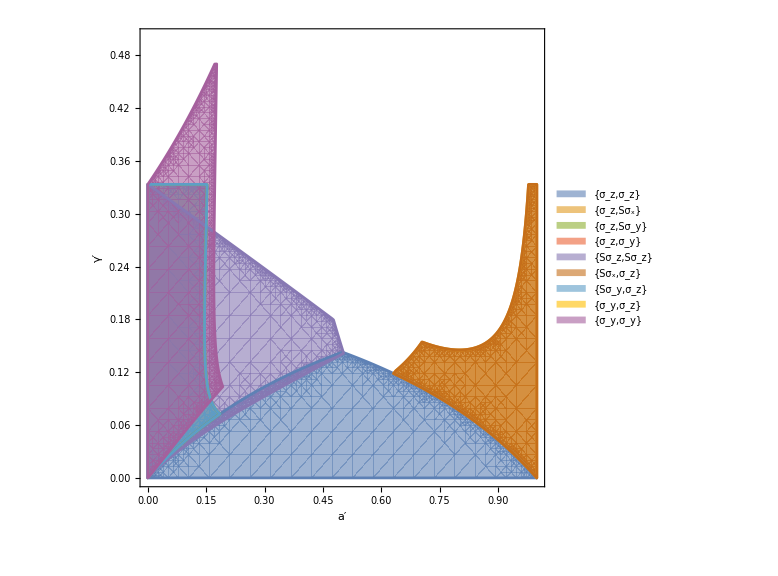

```mathematica
inequalities=eq[[;;,3]];
numRegions=Length[inequalities];
colors=Table[ColorData[97,i],{i,1,numRegions}];
labels=Table["Region "<>ToString[i],{i,1,numRegions}];

textures={HatchFilling[0],
HatchFilling[Pi/2],
HatchFilling[Pi/4],
HatchFilling[-Pi/4],
HatchFilling[Pi/8,2],
HatchFilling[Pi/3,2],
HatchFilling[0,2],
HatchFilling[Pi/2,2],
HatchFilling[Pi/4,2],HatchFilling[-Pi/4,2]};

r = RegionPlot[inequalities,{a′,0,1},{γ′,0,.5},PlotStyle->Table[{Opacity[0.6,colors[[i]]],textures[[i]]},{i,1,numRegions}],PlotLegends->Table[ToString[D4Sym[[e]],TraditionalForm],{e,eq[[;;,1]]}],FrameLabel->{"a′","γ′"},ImageSize->Large,MaxRecursion->6]
```

```mathematica
stableEquilibria =Table[{v[[1,1]],v[[2]]} ,{v,eq[[{2,3},{2,3}]]}];
```

```mathematica
stableEquilibria
```

{{a′+5 γ′-3 a′ γ′,(a′==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404&&γ′+AlgebraicNumber-0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{-59/160,1171/2400,-637/2400,17/480,1/480,1/2400}]-0.11895541459375736==0)||(3 γ′≤1&&(3 a′≥5||(a′>Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&1+3 a′ γ′≤a′+5 γ′)))||((-1+a′)/(-5+3 a′)≤γ′&&((a′>Root0.630Root[25-220 #1+484 #1^2-354 #1^3+60 #1^4+9 #1^6&,2]0.6300756617312404&&a′≤Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&(a′ (-10+a′+11 a′^2))/(5-7 a′)^2+6 √2 √((a′^3 (5-10 a′+4 a′^2+a′^3))/(5-7 a′)^4)+γ′≤0)||(a′>Root0.705Root[-200+1180 #1-2462 #1^2+2481 #1^3-1400 #1^4+392 #1^5&,2]0.7049464812615678&&a′≤Root0.979Root[16-40 #1-143 #1^2+162 #1^3+9 #1^4&,4]0.9786810237137125&&8 √((a′^2 (32-92 a′+112 a′^2-75 a′^3+23 a′^4))/(8-7 a′)^4)+γ′≤(32-60 a′+68 a′^2-39 a′^3)/(8-7 a′)^2)))},{1+2 γ′+a′ (-1+3 γ′),(a′==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&3 γ′==1)||(8+3 a′==3 √5+√(151-66 √5)&&√(151-66 √5) (7+3 √5)+60 γ′==23+3 √5)||(3 √5+2 a′>7&&((a′<Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094&&(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2+6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)≤γ′&&3 γ′≤1)||(a′>0&&8+3 a′<3 √5+√(151-66 √5)&&a′/(2+3 a′)≤γ′&&6 √2 √((a′^3 (-1+8 a′-8 a′^2+a′^3))/(2-7 a′)^4)+γ′≤(a′ (-2+23 a′-11 a′^2))/(2-7 a′)^2)))||(3 γ′≤1&&(((2+3 a′) γ′≥a′&&3 √5+2 a′≤7)||2+3 a′≤0))}}

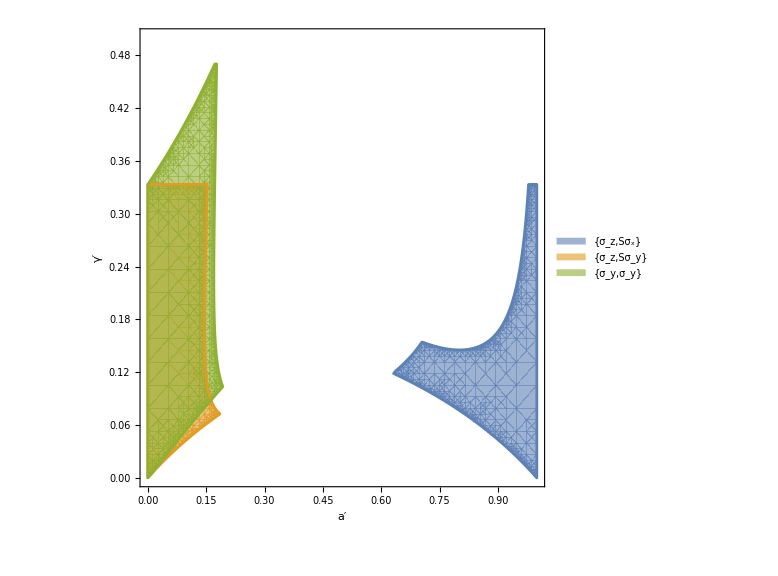

```mathematica
inequalities=eq[[{2,3,9},3]];
numRegions=Length[inequalities];
colors=Table[ColorData[97,i],{i,1,numRegions}];
labels=Table["Region "<>ToString[i],{i,1,numRegions}];

textures={HatchFilling[0],
HatchFilling[Pi/2],
HatchFilling[Pi/4]};

r = RegionPlot[inequalities,{a′,0,1},{γ′,0,.5},PlotStyle->Table[{Opacity[0.6,colors[[i]]],textures[[i]]},{i,1,numRegions}],PlotLegends->Table[ToString[D4Sym[[e]],TraditionalForm],{e,eq[[{2,3,9},1]]}],FrameLabel->{"a′","γ′"},ImageSize->Large,MaxRecursion->6]
```

```mathematica
f1=stableEquilibria[[1,1]]
f2=stableEquilibria[[2,1]]
```

1/4 (4-a′^2+2 a′ (3+√(1-a′) √γ′-4 γ′)+8 γ′)

1/4 (4-a′^2+8 γ′-2 a′ (-3+√(1-a′) √γ′+4 γ′))

```mathematica
Reduce[D[f1,a′]==0&&D[f1,γ′]==0&&a′<1&&γ′>0,{a′,γ′},Reals]  (* ->False*)
Reduce[D[f2,a′]==0&&D[f2,γ′]==0&&a′<1&&γ′>0,{a′,γ′},Reals]  (* ->False*)
```

False

False

```mathematica
BoundedRegionQ[ImplicitRegion[#[[2]],{a′,γ′}]]&/@stableEquilibria
```

{False,True}

```mathematica
vars={a′,γ′};
branches[reg_]:=If[Head[reg]===Or,List@@reg,{reg}];
maxOne[{f_,reg_}]:=Max[MaxValue[{f,#},vars]&/@branches[reg]];
globalMax=Max[maxOne/@stableEquilibria]
```

$Aborted